```mathematica
(*Import qPCR data and the original spreadsheet containing all the ID information*)
```

```mathematica
data=Import["./Downloads/Results.csv","csv"];
infor=Import["./Downloads/GAPREQ-16023.csv","csv"];
```

```mathematica
(*Simplify the information*)
```

```mathematica
less={};
Do[AppendTo[less,Flatten[{infor[[n]][[1]],infor[[n]][[6]]}]],{n,1,45}]
```

```mathematica
(*Merge the Root ID and Sample ID*)
```

```mathematica
new={};
AppendTo[new,{"Sample ID","Original Quant","Root ID"}];
Do[AppendTo[new,{data[[n]][[2]],data[[n]][[6]],StringInsert[StringReplace[less[[Flatten[Position[Transpose[less][[1]],data[[n]][[2]]]]]][[1]][[2]],"-"-> ""],"H",1]}],{n,2,Length[data]}]
```

```mathematica
Length[new]
```

81

```mathematica
(*Import the reads counts for H4015 and H4023*)
```

```mathematica
h4023=Import["./Downloads/external_IDs_and_sequencing_reads_count_control_H4023.csv","csv"];
h4015=Import["./Downloads/external_IDs_and_sequencing_reads_count_case_H4015.csv","csv"];
```

```mathematica
{"SM-HAV4H",38.25877007,"HSM5MD5X"},{"SM-HAV4I",5.693076243,"HSM67VDR"}
```

```mathematica
repli={};
Do[AppendTo[repli,new[[Flatten[Position[Transpose[new][[3]],Union[Transpose[new][[3]]][[n]]]]]]],{n,1,44}]
```

```mathematica
repli[[1]]
```

{{SM-HAV4H,27.1619,HSM5MD5X},{SM-HAV4H,38.2588,HSM5MD5X}}

```mathematica
(*handle all the replicates*)
```

```mathematica
repli1={};
Do[If[Length[repli[[n]]]>1,AppendTo[repli1,{repli[[n]][[1]][[1]],(repli[[n]][[1]][[2]]+repli[[n]][[2]][[2]])/2,repli[[n]][[1]][[3]]}]],{n,1,Length[repli]}]
Do[If[Length[repli[[n]]]<2,AppendTo[repli1,{repli[[n]][[1]][[1]],repli[[n]][[1]][[2]],repli[[n]][[1]][[3]]}]],{n,1,Length[repli]}]
```

```mathematica
(*For H4015*)
```

```mathematica
comp4015={};
AppendTo[comp4015,{"HSM5MD5X_P",39754946,38.25877007}];
Do[If[Length[Flatten[Position[Transpose[repli1][[3]],h4015[[n]][[1]]]]]>0,AppendTo[comp4015,{h4015[[n]][[1]],h4015[[n]][[2]],repli1[[Flatten[Position[Transpose[repli1][[3]],h4015[[n]][[1]]]]]][[1]][[2]]}]],{n,2,Length[h4015]}]
```

```mathematica
p4015={};
line={};Do[AppendTo[line,{comp4015[[n]][[2]],comp4015[[n]][[3]]}],{n,1,Length[comp4015]}]
```

```mathematica
Length[Flatten[line]]
```

44

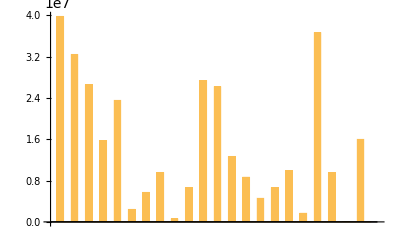

```mathematica
BarChart[Flatten[line]]
```

```mathematica
org1={};
Do[AppendTo[org1,{Flatten[line][[2n-1]],0}],{n,1,22}]
org2={};
Do[AppendTo[org2,{Flatten[line][[2n]],0}],{n,1,22}]
```

```mathematica
org={};
AppendTo[org,Flatten[org1]];
AppendTo[org,Flatten[org2]];
```

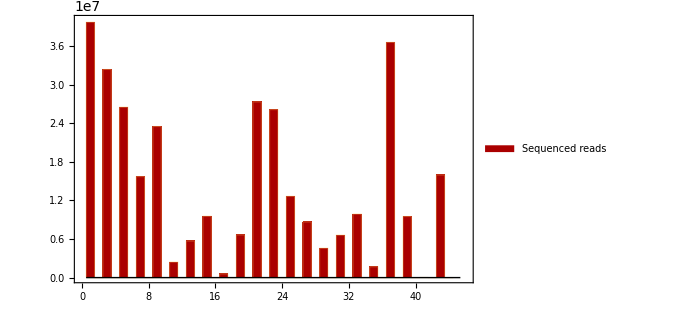

```mathematica
Plot3=BarChart[org[[1]],BarSpacing->{0,1},Frame->Left,FrameTicks->All,BarOrigin->Bottom,ChartStyle->{Darker[Red]},PlotRange->{{0,46},{0,40000000}},ImageSize->500,BaseStyle->{FontWeight->"Bold",FontSize->12},AxesStyle->Directive[Black,12],ChartLegends->{"Sequenced reads"}]
```

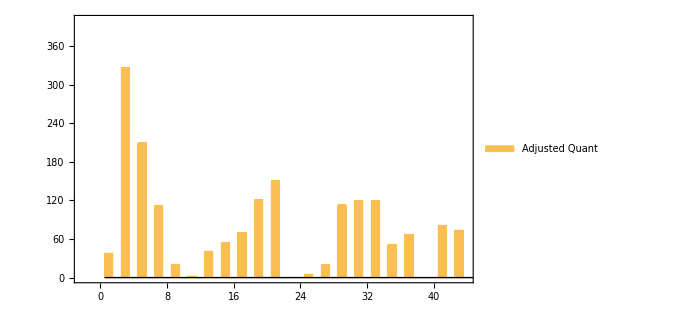

```mathematica
axis=BarChart[org[[2]],BarSpacing->{0,1},FrameTicks->All,Frame->Right,BarOrigin->Bottom,PlotRange->{{-2.2,43.8},{0,400}},Frame->{False,False,False,True},FrameStyle->Darker[Blue],BaseStyle->{FontWeight->"Bold",FontSize->12},ImageSize->500,ChartLegends->{"Adjusted Quant"}]
```

```mathematica
(*For H4023*)
```

```mathematica
{"SM-HAV4H",38.25877007,"HSM5MD5X"},{"SM-HAV4I",5.693076243,"HSM67VDR"}
```

```mathematica
comp4023={};
AppendTo[comp4023,{"HSM67VDR_P",21426526,5.6930}];
Do[If[Length[Flatten[Position[Transpose[repli1][[3]],h4023[[n]][[1]]]]]>0,AppendTo[comp4023,{h4023[[n]][[1]],h4023[[n]][[2]],repli1[[Flatten[Position[Transpose[repli1][[3]],h4023[[n]][[1]]]]]][[1]][[2]]}]],{n,2,Length[h4023]}]
```

```mathematica
p4023={};
line={};Do[AppendTo[line,{comp4023[[n]][[2]],comp4023[[n]][[3]]}],{n,1,Length[comp4023]}]
```

```mathematica
Length[Flatten[line]]
```

44

```mathematica
org1={};
Do[AppendTo[org1,{Flatten[line][[2n-1]],0}],{n,1,22}]
org2={};
Do[AppendTo[org2,{Flatten[line][[2n]],0}],{n,1,22}]
```

```mathematica
org={};
AppendTo[org,Flatten[org1]];
AppendTo[org,Flatten[org2]];
```

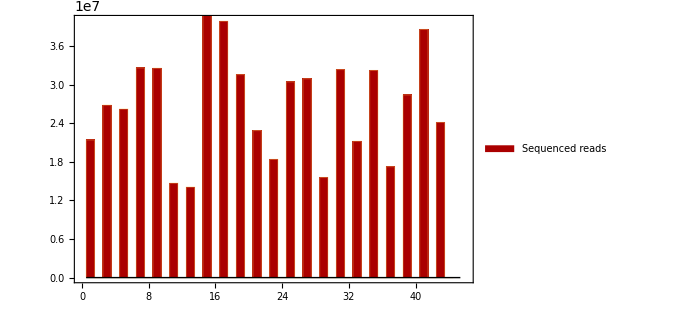

```mathematica
Plot3=BarChart[org[[1]],BarSpacing->{0,1},Frame->Left,FrameTicks->All,BarOrigin->Bottom,ChartStyle->{Darker[Red]},PlotRange->{{0,46},{0,40000000}},ImageSize->500,BaseStyle->{FontWeight->"Bold",FontSize->12},AxesStyle->Directive[Black,12],ChartLegends->{"Sequenced reads"}]
```

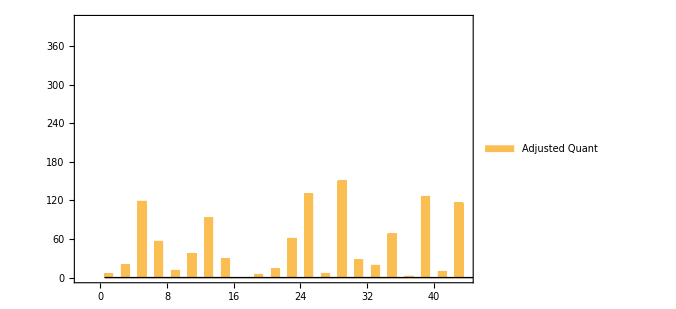

```mathematica
axis=BarChart[org[[2]],BarSpacing->{0,1},FrameTicks->All,Frame->Right,BarOrigin->Bottom,PlotRange->{{-2.2,43.8},{0,400}},Frame->{False,False,False,True},FrameStyle->Darker[Blue],BaseStyle->{FontWeight->"Bold",FontSize->12},ImageSize->500,ChartLegends->{"Adjusted Quant"}]
```